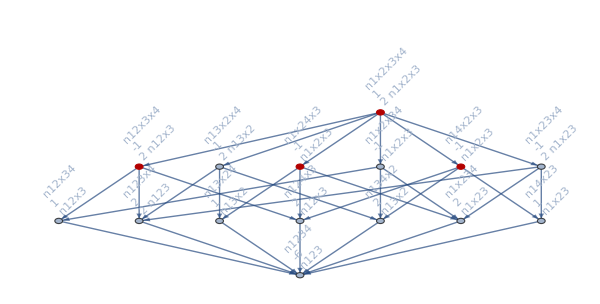

```mathematica
Graph[MobiusGraph4[allKey,allGraphs],GraphHighlight->{n1x2x3x4,n1x24x3,n12x3x4,n14x2x3}]
```

```mathematica
Table[s->0,{s,fullSymbols4}]
```

{v1x2x3x4→0,v1x2x34→0,v1x23x4→0,v1x24x3→0,v12x3x4→0,v13x2x4→0,v14x2x3→0,v12x34→0,v13x24→0,v14x23→0,v1x234→0,v123x4→0,v124x3→0,v134x2→0,v1234→0}

```mathematica
fullSymbols4/.{v1x2x3x4->1,v1x2x34->0,v1x23x4->0,v1x24x3->1,v12x3x4->1,v13x2x4->0,v14x2x3->1,v12x34->0,v13x24->0,v14x23->0,v1x234->0,v123x4->0,v124x3->0,v134x2->0,v1234->0}
```

{1,0,0,1,1,0,1,0,0,0,0,0,0,0,0}

```mathematica
Select[Keys[allGraphs4],FullVector4[#]=={1,0,0,1,1,0,1,0,0,0,0,0,0,0,0}&]
```

{}

```mathematica
ExpressionToTable2[reduced]
```

f12==-1+n12
f123==2-n12+n123-n13-n23
f124==2-n12+n124-n14-n24
f13==-1+n13
f134==2-n13+n134-n14-n34
f14==-1+n14
f23==-1+n23
f234==2-n23+n234-n24-n34
f24==-1+n24
f34==-1+n34
f12♁34==1-n12-n34+n12♁34
f13♁24==1-n13-n24+n13♁24
f14♁23==1-n14-n23+n14♁23
fOverHat[0]==-6+2 n12-n123-n124+2 n13-n134+2 n14+2 n23-n234+2 n24+2 n34-n12♁34-n13♁24-n14♁23+nOverHat[0]
fOverHat[1]==1
nOverHat[1]==1